# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Eigenvectors

```mathematica
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
(*Floquet parameters*)
J=513;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
```

Generating coherent states over 31397 points...

```mathematica
rot=MatrixExp[I(α/2)ops[[3]]];
```

```mathematica
α=Pi/2.;
k=13.7;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
(*mat=ConjugateTranspose[rot].Floq[J,α,k].rot;*)
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
{rM,rm}={MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.547664,0.418804}

```mathematica
(rM-0.38)/(0.53-0.38)
(rm-0.38)/(0.53-0.38)
```

1.11776

0.258694

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3,Background->White]
```

-Graphics-

## Eigenvalues

```mathematica
Pi/2.
```

1.5708

```mathematica
(*Floquet parameters*)
J=2000;
α=0.84;
k=21.;
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.535468,0.534997}

```mathematica
phases=Sort[Arg[eigenvalM]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
```

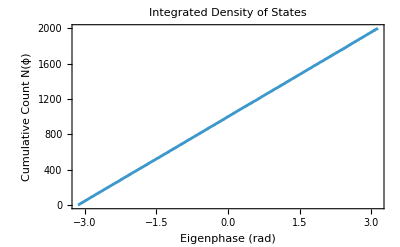

```mathematica
(*3. Plot the staircase function*)
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True,ImageSize->400]
```

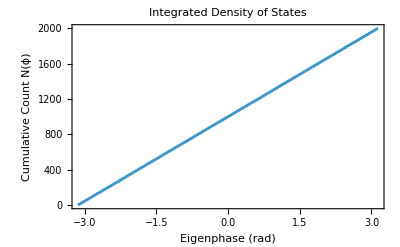

```mathematica
phases=Sort[Arg[eigenvalm]];
data=Table[{phases[[i]],i},{i,1,Length[phases]}];
ListPlot[data,Frame->True,FrameLabel->{"Eigenphase (rad)","Cumulative Count N(ϕ)"},PlotLabel->"Integrated Density of States",Joined->True,ImageSize->400]
```

```mathematica
phases=Sort[Arg[eigenvalm]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

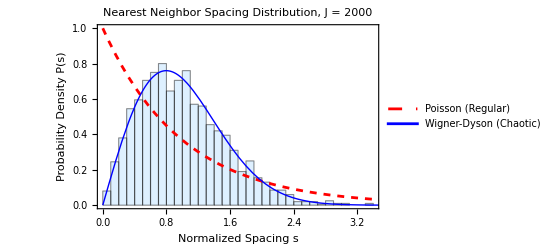

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,20.0,0.25];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

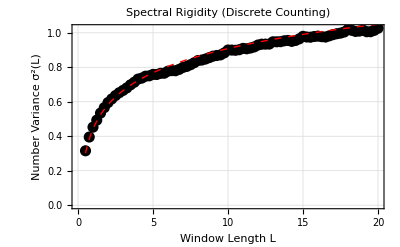

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

```mathematica
goe[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
gue[L_]:=(1/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

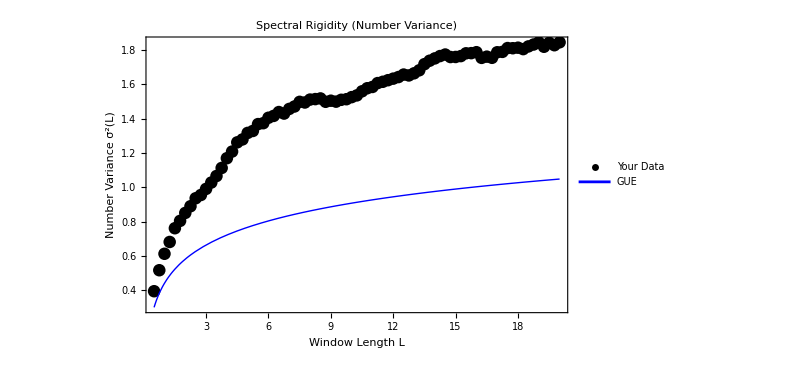

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

```mathematica
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

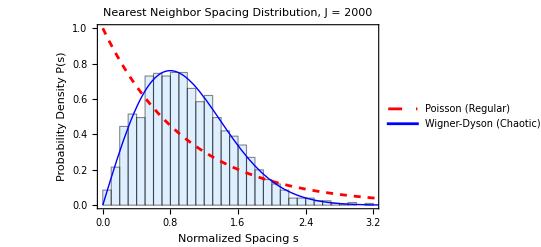

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

```mathematica
(*1. Create an efficient counting function using Interpolation*)(*This maps energy->index.n(E)*)
n=Length[unfolded];
staircase=Interpolation[Transpose[{unfolded,Range[n]}],InterpolationOrder->1];
```

```mathematica
(*2. Define the range of L and the spectrum boundaries*)
eMin=Min[unfolded];
eMax=Max[unfolded];
Lvalues=Range[0.5,20.0,0.25];
(*crucial:'unfolded' must be defined before running this*)
DistributeDefinitions[unfolded];
```

```mathematica
(*3. Parallel Calculation of Sigma^2(L)*)
sigmaData=ParallelTable[Module[{centers,counts,eMin,eMax},
eMin=Min[unfolded];
eMax=Max[unfolded];
(*Define centers for the sliding window*)(*Step size 0.2 gives good statistics without being too slow*)
centers=Range[eMin+L/2,eMax-L/2,0.2];
(*Count how many levels fall in each window*)
counts=Table[Count[unfolded,x_/;(c-L/2<=x<=c+L/2)],{c,centers}];
(*Return the pair {L,Variance}*)
{L,Variance[counts]}],{L,Lvalues},Method->"CoarsestGrained"];
```

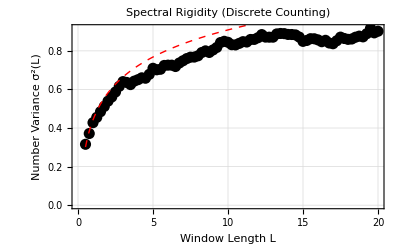

```mathematica
(*4. Plot to check the fix*)
(*Positive parity*)
ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Discrete Counting)",GridLines->Automatic,Epilog->{Red,Dashed,Line[Table[{L,(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8)},{L,0.5,20,0.1}]]}]
```

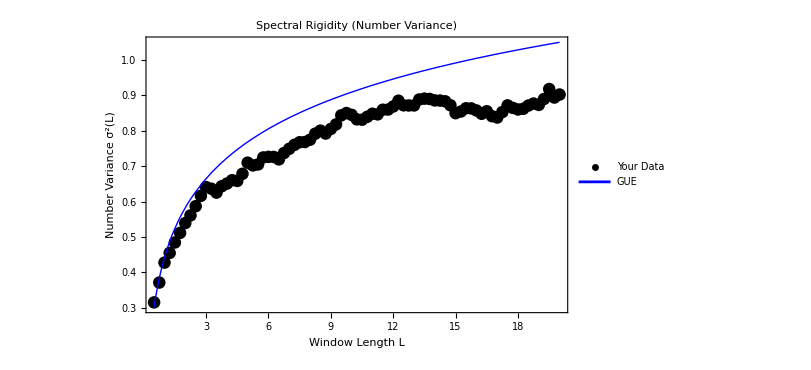

```mathematica
(*5. Plot*)
(*Positive parity*)
Show[ListPlot[sigmaData,PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Your Data"}],Plot[{goe[L]},{L,0.5,20},PlotStyle->{{Blue,Thick}},PlotLegends->{"GUE ","GOE (Chaotic)"}],Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Spectral Rigidity (Number Variance)",PlotRange->All,ImageSize->600]
```

# Number variance

## single realization

```mathematica
ClearAll[EigenvaluesList,PrepareCircularUnfolding,MakeCountLE,Sigma2Data,Sigma2GOEAsympt];
EigenvaluesList[obj_]:=If[MatrixQ[obj],Eigenvalues[obj,Method->"Direct"],obj];
PrepareCircularUnfolding[eigs_List]:=Module[{phases,n,x,ms,x2},phases=Sort@Mod[Arg[eigs],2 Pi];
n=Length[phases];
x=(n/(2 Pi)) phases;
ms=Mean[Differences@Join[x,{x[[1]]+n}]];
x=x/ms;
x2=Join[x,x+n];
<|"n"->n,"phases"->phases,"x"->x,"x2"->x2,"meanSpacingRaw"->ms|>];
MakeCountLE[x2_List]:=Module[{xx=Developer`ToPackedArray@N@x2,m=Length[x2]},Compile[{{z,_Real}},Module[{lo=1,hi=m,mid=0},While[lo<=hi,mid=Quotient[lo+hi,2];
If[xx[[mid]]<=z,lo=mid+1,hi=mid-1];];
hi],CompilationTarget->"WVM",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->False]];
Sigma2Data[obj_,Lvalues_List,nCenters_:4000,seed_:1,useParallel_:True]:=Module[{eigs,spec,n,x2,countLE,centers,Lvals,sigma2},eigs=EigenvaluesList[obj];
spec=PrepareCircularUnfolding[eigs];
n=spec["n"];x2=spec["x2"];
Lvals=Select[N@Lvalues,0<#<n&];
BlockRandom[SeedRandom[seed];centers=RandomReal[{0,n},nCenters]];
countLE=MakeCountLE[x2];
sigma2=With[{cl=countLE,c=centers},Function[{L},Module[{counts},counts=cl[c+L]-cl[c];
{L,Mean[counts],Variance[counts]}]]];
If[useParallel,ParallelMap[sigma2,Lvals,Method->"CoarsestGrained"],Map[sigma2,Lvals]]];
Sigma2GOEAsympt[L_?NumericQ]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);
```

```mathematica
(*Code to plot the Staircase Function*)
Clear[TestStaircase];
TestStaircase[eigs_]:=Module[{phases=Sort@Mod[Arg[eigs],2 Pi],n,staircase,smooth},
n=Length[phases];
staircase=Transpose[{phases,Range[n]}]];
```

```mathematica
J=500;
α=0.84;
δ=0.001;
k=21.;
k=RandomReal[{k-δ,k+δ}];
```

```mathematica
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
eigenvalM=Eigenvalues[matM,Method->"Direct"];
eigenvalm=Eigenvalues[matm,Method->"Direct"];
```

```mathematica
dataM=TestStaircase[eigenvalM];
datam=TestStaircase[eigenvalm];
```

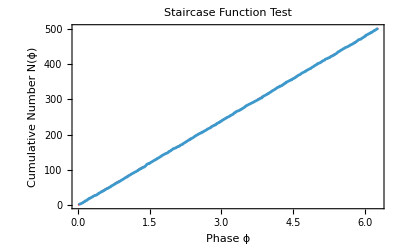

-Graphics-

```mathematica
ListLinePlot[dataM,Prolog->{Red,Dashed,Line[{{0,0},{2 Pi,Length[eigenvalM]}}]},Frame->True,FrameLabel->{"Phase ϕ","Cumulative Number N(ϕ)"},PlotLabel->"Staircase Function Test",BaseStyle->{FontSize->14}]
ListLinePlot[dataM,Prolog->{Red,Dashed,Line[{{0,0},{2 Pi,Length[eigenvalM]}}]},Frame->True,FrameLabel->{"Phase ϕ","Cumulative Number N(ϕ)"},PlotLabel->"Staircase Function Test",BaseStyle->{FontSize->14}]
```

```mathematica
(*Code to test the Mean Spacing*)
TestMeanSpacing[eigs_]:=Module[{unfoldedSpec,spacings,meanS},
unfoldedSpec=PrepareCircularUnfolding[eigs];
(*Calculate differences between adjacent unfolded levels*)
spacings=Differences[unfoldedSpec["x"]];
(*Add the periodic boundary wrap-around spacing*)
AppendTo[spacings,unfoldedSpec["n"]-Last[unfoldedSpec["x"]]+First[unfoldedSpec["x"]]];
meanS=Mean[spacings];
Print["Mean Level Spacing: ",meanS];
Print["Deviation from 1.0: ",Abs[1.0-meanS]];];
```

```mathematica
(*Code to plot NNSD against Wigner Surmise*)
TestNNSD[eigs_]:=Module[{unfoldedSpec,spacings,wignerSurmise,s},
unfoldedSpec=PrepareCircularUnfolding[eigs];
spacings=Differences[unfoldedSpec["x"]];
AppendTo[spacings,unfoldedSpec["n"]-Last[unfoldedSpec["x"]]+First[unfoldedSpec["x"]]];
wignerSurmise=(Pi/2)*s*Exp[-(Pi/4)*s^2];
Show[Histogram[spacings,{0,4,0.1},"PDF",ChartStyle->EdgeForm[Gray],PlotTheme->"Detailed"],Plot[wignerSurmise,{s,0,4},PlotStyle->{Red,Thickness[0.005]}],Frame->True,FrameLabel->{"Spacing s","P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution",BaseStyle->{FontSize->14},PlotRange->All]]
```

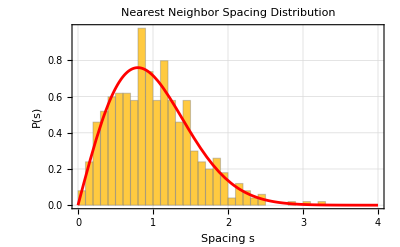

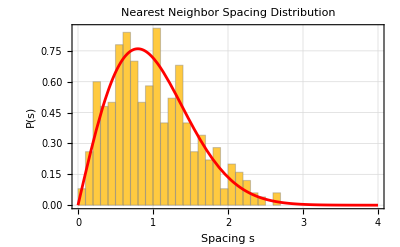

```mathematica
TestNNSD[eigenvalM]
TestNNSD[eigenvalm]
```

```mathematica
(* ======*)(*Quantifiable Unfolding Tests (Local Spacing& KS Test)*)(* ==========================================================*)
Clear[QuantifyUnfolding];
QuantifyUnfolding[eigs_,windowSize_:50]:=Module[{unfoldedSpec,spacings,n,localMeans,maxDev,meanDev,sortedS,empCDF,wignerCDF,ksStatistic},(*1. Prepare Spacings*)
unfoldedSpec=PrepareCircularUnfolding[eigs];
n=unfoldedSpec["n"];
spacings=Differences[unfoldedSpec["x"]];
AppendTo[spacings,n-Last[unfoldedSpec["x"]]+First[unfoldedSpec["x"]]];
(*-----------------------------------*)(*TEST 1:LOCAL MEAN SPACING*)(*--------------------------------------------------------*)(*Compute the moving average of the spacings*)
localMeans=MovingAverage[spacings,windowSize];
(*Quantify the deviations from 1.0*)maxDev=Max[Abs[localMeans-1.0]];
meanDev=Mean[Abs[localMeans-1.0]];
Print["--- LOCAL MEAN SPACING TEST (Window = ",windowSize,") ---"];
Print["Maximum deviation from 1.0 : ",maxDev];
Print["Average deviation from 1.0 : ",meanDev];
(*--------------------------------------------------------*)(*TEST 2:KOLMOGOROV-SMIRNOV TEST (INTEGRATED P(S))*)(*--------------------------------------------------------*)sortedS=Sort[spacings];
(*Empirical CDF:k/N for the k-th sorted spacing*)empCDF=Range[1,n]/n;
(*Theoretical Wigner CDF*)wignerCDF=1-Exp[-(Pi/4)*sortedS^2];
(*KS Statistic:Maximum vertical distance between the two CDFs*)ksStatistic=Max[Abs[empCDF-wignerCDF]];
Print["\n--- KOLMOGOROV-SMIRNOV TEST (Cumulative P(s)) ---"];
Print["KS Statistic (Max Distance): ",ksStatistic];
If[ksStatistic<0.05,Print[Style["Result: EXCELLENT MATCH (Unfolding is highly uniform).",Darker[Green,0.5]]],Print[Style["Result: POOR MATCH (Check unfolding or dynamics regime).",Red]]];
(*Optional:Plot the CDFs to visually confirm the KS test*)Print[ListPlot[{Transpose[{sortedS,empCDF}],(*Empirical:Blue Points*)Transpose[{sortedS,wignerCDF}]   (*Theoretical:Red Line*)},Joined->{False,True},PlotStyle->{Directive[PointSize[Medium],Blue],Directive[Thickness[0.005],Red]},Frame->True,FrameLabel->{"Spacing s","Cumulative Probability CDF(s)"},PlotLabel->"Integrated P(s): Empirical vs Wigner",BaseStyle->{FontSize->14},PlotLegends->{"Empirical Data","Wigner Theory"},ImageSize->550]];]
```

```mathematica
Ucoe=RandomVariate[CircularOrthogonalMatrixDistribution[999]];
eigenval=Eigenvalues[Ucoe,Method->"Direct"];
```

--- LOCAL MEAN SPACING TEST (Window = 100) ---

Maximum deviation from 1.0 : 0.0353741

Average deviation from 1.0 : 0.00782248

--- KOLMOGOROV-SMIRNOV TEST (Cumulative P(s)) ---

KS Statistic (Max Distance): 0.0159625

Result: EXCELLENT MATCH (Unfolding is highly uniform).

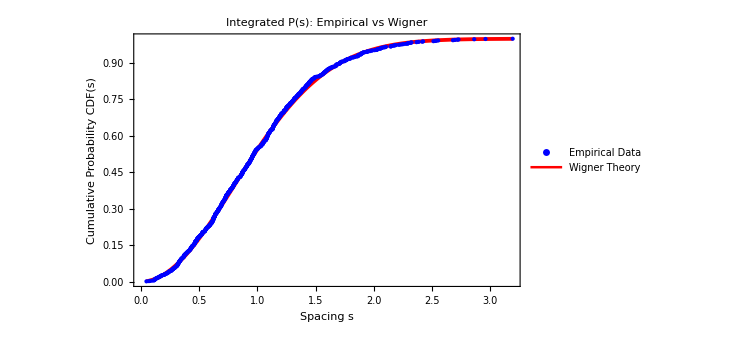

```mathematica
QuantifyUnfolding[eigenval,100]
```

--- LOCAL MEAN SPACING TEST (Window = 100) ---

Maximum deviation from 1.0 : 0.030524

Average deviation from 1.0 : 0.00877515

--- KOLMOGOROV-SMIRNOV TEST (Cumulative P(s)) ---

KS Statistic (Max Distance): 0.0236512

Result: EXCELLENT MATCH (Unfolding is highly uniform).

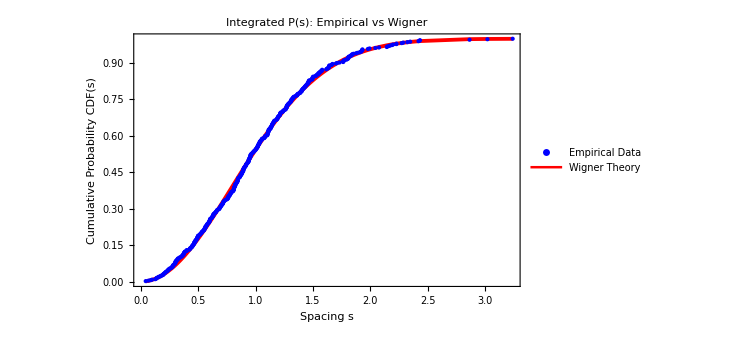

```mathematica
QuantifyUnfolding[eigenvalM,100]
```

--- LOCAL MEAN SPACING TEST (Window = 100) ---

Maximum deviation from 1.0 : 0.025424

Average deviation from 1.0 : 0.00849256

--- KOLMOGOROV-SMIRNOV TEST (Cumulative P(s)) ---

KS Statistic (Max Distance): 0.042049

Result: EXCELLENT MATCH (Unfolding is highly uniform).

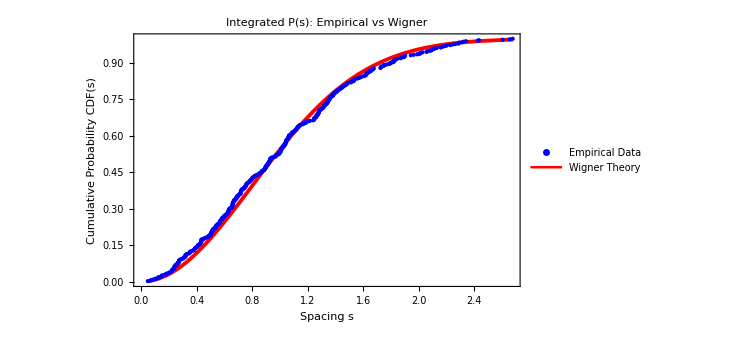

```mathematica
QuantifyUnfolding[eigenvalm,100]
```

```mathematica
(*======================Fluctuation Analysis======================*)
ClearAll[GetFluctuations];
GetFluctuations[specData_Association]:=Module[{x,n,delta},x=specData["x"];
n=specData["n"];
(*delta_i=(i-0.5)-x_i*)
delta=Table[(i-0.5)-x[[i]],{i,1,n}];
<|"delta"->delta,"n"->n|>];
```

```mathematica
(*1. Assuming you have a matrix'mat'*)
spec=PrepareCircularUnfolding[eigenvalM];
(*2. Get the fluctuations*)
fluc=GetFluctuations[spec];
```

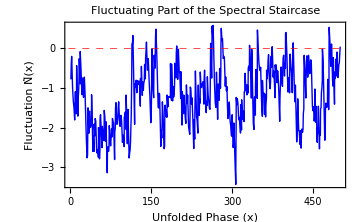

```mathematica
(*Combine the unfolded phases (x) with their corresponding fluctuations (delta)*)
fluctuationPlotData=Transpose[{spec["x"],fluc["delta"]}];
(*Plot the result*)
ListLinePlot[fluctuationPlotData,PlotStyle->Directive[AbsoluteThickness[1],Blue],Frame->True,FrameLabel->{"Unfolded Phase (x)","Fluctuation \!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},PlotLabel->"Fluctuating Part of the Spectral Staircase",ImageSize->Medium,(*Force the y-axis to be centered around 0 to easily spot trends*)PlotRange->All,GridLines->{None,{0}},GridLinesStyle->Directive[Red,Dashed]]
```

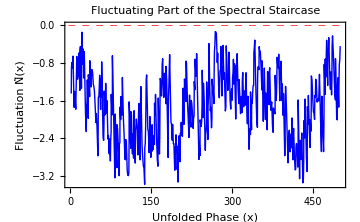

```mathematica
(*1. Assuming you have a matrix'mat'*)
spec=PrepareCircularUnfolding[eigenvalm];
(*2. Get the fluctuations*)
fluc=GetFluctuations[spec];
(*Combine the unfolded phases (x) with their corresponding fluctuations (delta)*)
fluctuationPlotData=Transpose[{spec["x"],fluc["delta"]}];
(*Plot the result*)
ListLinePlot[fluctuationPlotData,PlotStyle->Directive[AbsoluteThickness[1],Blue],Frame->True,FrameLabel->{"Unfolded Phase (x)","Fluctuation \!\(\*OverscriptBox[\(N\), \(~\)]\)(x)"},PlotLabel->"Fluctuating Part of the Spectral Staircase",ImageSize->Medium,(*Force the y-axis to be centered around 0 to easily spot trends*)PlotRange->All,GridLines->{None,{0}},GridLinesStyle->Directive[Red,Dashed]]
```

```mathematica
(*======================Execution (Floquet sector+COE benchmark)======================*)
Lvalues=Range[0.2,50.0,0.2];
```

```mathematica
AbsoluteTiming[sigmaDataCOE=Sigma2Data[eigenvalM,Lvalues,4000,2,True];]
```

{3.07003,Null}

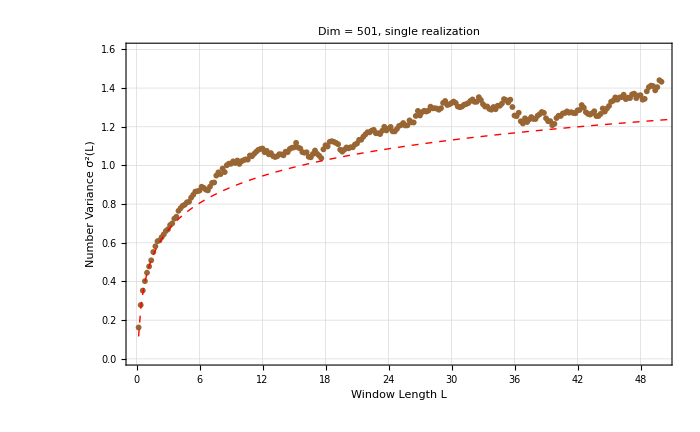

```mathematica
plotCOE=ListPlot[sigmaDataCOE[[All,{1,3}]],PlotStyle->{Brown,PointSize[0.006]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},FrameStyle->Directive[Black,15],PlotLabel->Style["Dim = "<>ToString[J+1]<>", single realization",20,Black],GridLines->Automatic,Epilog->{Red,Dashed,Line@Table[{L,Sigma2GOEAsympt[L]},{L,0.2,400,0.2}]},PlotRange->{All,{0,1.6}},ImageSize->700]
```

```mathematica
AbsoluteTiming[sigmaDataCOE=Sigma2Data[eigenvalm,Lvalues,1000,2,True];]
```

{0.781645,Null}

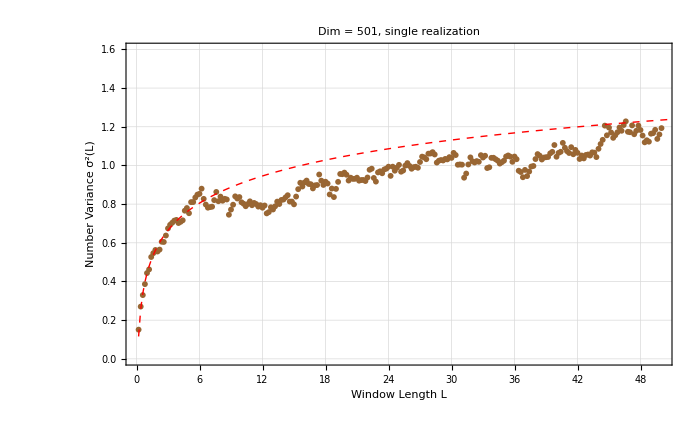

```mathematica
plotCOE=ListPlot[sigmaDataCOE[[All,{1,3}]],PlotStyle->{Brown,PointSize[0.006]},Frame->True,FrameLabel->{"Window Length L","Number Variance \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},FrameStyle->Directive[Black,15],PlotLabel->Style["Dim = "<>ToString[J+1]<>", single realization",20,Black],GridLines->Automatic,Epilog->{Red,Dashed,Line@Table[{L,Sigma2GOEAsympt[L]},{L,0.2,400,0.2}]},PlotRange->{All,{0,1.6}},ImageSize->700]
```

```mathematica
ClearAll[CircularUnfold];
CircularUnfold[eigenvalues_List]:=Module[{phases=Sort[Mod[Arg[eigenvalues],2 Pi]],n,unfolded,extended},
n=Length[phases];
(*2. Linear Unfolding:map to uniform density ρ=1*)
unfolded=(n/(2 Pi))*phases;
(*3. Periodic Extension:duplicate spectrum to handle wrap-around for large L*)
extended=Join[unfolded,unfolded+n];
<|"N"->n,"Unfolded"->unfolded,"Extended"->extended|>];
```

```mathematica
(*ClearAll[CompileLevelCounter];
CompileLevelCounter[extendedSpectrum_List]:=Module[{packedArray,m},
packedArray=Developer`ToPackedArray[N[extendedSpectrum]];
m=Length[packedArray];
Compile[{{z,_Real}},Module[{lo=1,hi=m,mid=0},While[lo<=hi,mid=Quotient[lo+hi,2];
If[packedArray[[mid]]<=z,lo=mid+1,hi=mid-1];];
hi],CompilationTarget->"WVM",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->False]];*)
```

```mathematica
ClearAll[CompileLevelCounterParallel];
CompileLevelCounterParallel[extendedSpectrum_List]:=Module[{packedArray,m},
packedArray=Developer`ToPackedArray[N[extendedSpectrum]];
m=Length[packedArray];
Compile[{{z,_Real}},Module[{lo=1,hi=m,mid=0},While[lo<=hi,mid=Quotient[lo+hi,2];
If[packedArray[[mid]]<=z,lo=mid+1,hi=mid-1];];
hi],CompilationTarget->"WVM",(*Set to "C" for maximum multi-core scaling if a C-compiler is present*)RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True (*Enables automatic multi-threading over the input list*)]];
```

```mathematica
(*ClearAll[ComputeSigma2];
ComputeSigma2[counterFunc_,nLevels_Integer,lValues_List,nSamples_Integer:5000,seed_Integer:42]:=Module[{validL,centers,computeForL},
(*Restrict L to physically meaningful bounds (L<N/2 to avoid symmetry reflection)*)
validL=Select[N[lValues],0<#<=(nLevels/2.0)&];
(*Generate stochastic continuous sampling grid over the fundamental domain*)
BlockRandom[SeedRandom[seed];
centers=RandomReal[{0,nLevels},nSamples];];
(*Function to compute variance for a single L*)
computeForL=Function[{L},Module[{counts},
(*Vectorized application of the counting function*)
counts=counterFunc[centers+L]-counterFunc[centers];
{L,Variance[counts]}]];
(*Map over all requested L values*)Map[computeForL,validL]];*)
```

```mathematica
ClearAll[ComputeSigma2Parallel];
ComputeSigma2Parallel[counterFunc_,nLevels_Integer,lValues_List,nSamples_Integer:5000,seed_Integer:42]:=Module[{validL,centers,computeForL},
validL=Select[N[lValues],0<#<=(nLevels/2.0)&];
BlockRandom[SeedRandom[seed];
centers=RandomReal[{0,nLevels},nSamples];];
computeForL=Function[{L},Module[{counts},counts=counterFunc[centers+L]-counterFunc[centers];
{L,Variance[counts]}]];
(*Distribute the evaluation of independent L values across CPU subkernels*)
ParallelMap[computeForL,validL,Method->"CoarsestGrained"]];
```

```mathematica
ClearAll[TheorySigma2COE];
TheorySigma2COE[l_?NumericQ]:=(2.0/Pi^2)*(Log[2.0 Pi*l]+EulerGamma+1.0-Pi^2/8.0);
```

```mathematica
Ucoe=RandomVariate[CircularOrthogonalMatrixDistribution[500]];
eigenval=Eigenvalues[Ucoe,Method->"Direct"];
```

```mathematica
(*1. Assume'eigs' is a list of complex eigenvalues from a COE matrix*)
unfoldData=CircularUnfold[eigenval];
(*2. Compile the fast counter using the periodically extended array*)
fastCounter=CompileLevelCounter[unfoldData["Extended"]];
(*3. Define the L domains (e.g.,from L=1 up to L=50)*)
lTestValues=Range[0.5,30.0,0.1];
```

```mathematica
(*(*4. Compute the numerical Number Variance using 10,000 sampling centers*)
numericalSigma2=ComputeSigma2[fastCounter,unfoldData["N"],lTestValues,1000];*)
```

```mathematica
AbsoluteTiming[numericalSigma2=ComputeSigma2Parallel[fastCounter,unfoldData["N"],lTestValues,4000];]
```

{3.63009,Null}

```mathematica
(*5. Compute the theoretical curve for comparison*)
theorySigma2={#,TheorySigma2COE[#]}&/@lTestValues;
```

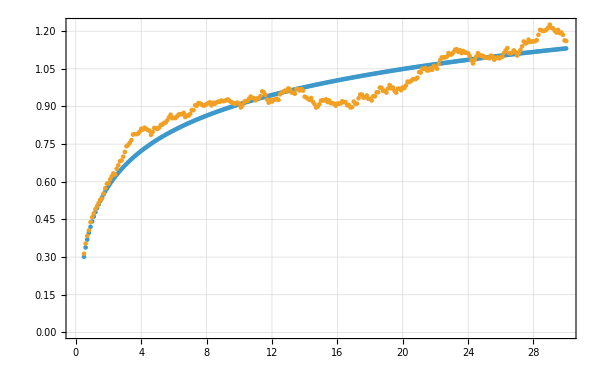

```mathematica
ListPlot[{theorySigma2,numericalSigma2},PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

## ensemble test

```mathematica
(*---CORE DEFINITIONS AND COMPILATIONS---*)
ClearAll[GetUnfoldedSpectrum,GenerateEnsembleSpectra,ComputeSigma2,EvaluateSpectrumSigma2,EnsembleSigma2FromSpectra,CompileContinuousSFF,EnsembleSFFFromSpectra];

GetUnfoldedSpectrum[jParam_,alphaParam_,kParam_]:=Module[{mat,matM,eigs,phases,effectiveDim,unfoldedSpectrum},mat=Floq[jParam,alphaParam,kParam];
matM=mat[[2;; ;;2,2;; ;;2]];
eigs=Eigenvalues[matM,Method->"Direct"];
phases=Sort[Mod[Arg[eigs],2 Pi]];
effectiveDim=Length[phases];
unfoldedSpectrum=(effectiveDim/(2 Pi))*phases;
<|"N"->effectiveDim,"Spectrum"->unfoldedSpectrum|>];

GenerateEnsembleSpectra[jParam_,alphaParam_,kList_List]:=ParallelTable[GetUnfoldedSpectrum[jParam,alphaParam,k],{k,kList},Method->"CoarsestGrained"];

ComputeSigma2[counterFunc_,nLevels_Integer,lValues_List,nSamples_Integer:2000,seed_Integer:42]:=Module[{validL,centers,computeForL},validL=Select[N[lValues],0<#<=(nLevels/2.0)&];
BlockRandom[SeedRandom[seed];
centers=RandomReal[{0,nLevels},nSamples];];
computeForL=Function[{L},Module[{counts,fixedMeanVariance},counts=counterFunc[centers+L]-counterFunc[centers];
fixedMeanVariance=Total[(counts-L)^2]/nSamples;
{L,fixedMeanVariance}]];
Map[computeForL,validL]];

ClearAll[CompileLevelCounter];
CompileLevelCounter[extendedSpectrum_List]:=Module[{packedArray,m},
packedArray=Developer`ToPackedArray[N[extendedSpectrum]];
m=Length[packedArray];
Compile[{{z,_Real}},Module[{lo=1,hi=m,mid=0},While[lo<=hi,mid=Quotient[lo+hi,2];
If[packedArray[[mid]]<=z,lo=mid+1,hi=mid-1];];
hi],CompilationTarget->"WVM",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->False]];
```

```mathematica
EvaluateSpectrumSigma2[spectrumData_,lValues_List,nSamples_Integer,seed_Integer]:=Module[{extendedSpectrum,fastCounter,sigma2Data},
extendedSpectrum=Join[spectrumData["Spectrum"]-spectrumData["N"],spectrumData["Spectrum"],spectrumData["Spectrum"]+spectrumData["N"]];
fastCounter=CompileLevelCounter[extendedSpectrum];
sigma2Data=ComputeSigma2[fastCounter,spectrumData["N"],lValues,nSamples,seed];
sigma2Data[[All,2]]];

EnsembleSigma2FromSpectra[spectraList_List,lValues_List,nSamples_Integer]:=Module[{nMatrices,ensembleVariances,meanSigma2,stdErrorSigma2},nMatrices=Length[spectraList];
DistributeDefinitions[CompileLevelCounter,ComputeSigma2,EvaluateSpectrumSigma2];
ensembleVariances=ParallelTable[EvaluateSpectrumSigma2[spectraList[[i]],lValues,nSamples,RandomInteger[{1,10^8}]],{i,nMatrices},Method->"CoarsestGrained"];
meanSigma2=Mean[ensembleVariances];
stdErrorSigma2=StandardDeviation[ensembleVariances]/Sqrt[nMatrices*1.0];
<|"LValues"->lValues,"MeanVariance"->meanSigma2,"StandardError"->stdErrorSigma2|>];

CompileContinuousSFF=Compile[{{unfoldedSpectrum,_Real,1},{tauValues,_Real,1}},
Module[{nLevels=Length[unfoldedSpectrum],tau,cosSum,sinSum},
Table[cosSum=Total[Cos[2.0*Pi*unfoldedSpectrum*tau]];
sinSum=Total[Sin[2.0*Pi*unfoldedSpectrum*tau]];
(cosSum^2+sinSum^2)/nLevels,{tau,tauValues}]],CompilationTarget->"WVM",RuntimeOptions->"Speed"];

EnsembleSFFFromSpectra[spectraList_List,tauLimit_Real,numPoints_Integer]:=Module[{nMatrices,tauValues,ensembleK,meanK,stdErrorK},nMatrices=Length[spectraList];
tauValues=Range[tauLimit/numPoints,tauLimit,tauLimit/numPoints];
DistributeDefinitions[CompileContinuousSFF];
ensembleK=ParallelTable[CompileContinuousSFF[spectraList[[i]]["Spectrum"],tauValues],{i,nMatrices},Method->"CoarsestGrained"];
meanK=Mean[ensembleK];
stdErrorK=StandardDeviation[ensembleK]/Sqrt[nMatrices*1.0];
<|"TauDomain"->tauValues,"MeanSFF"->meanK,"StandardError"->stdErrorK|>];

CompileLDelta3=Compile[{{extendedSpectrum,_Real,1},{centers,_Real,1},{L,_Real}},Module[{c,n,M0,M1,M2,a,b,delta3Sum=0.0,y,sumY,sumY2,sumN2Y,i,j},For[i=1,i<=Length[centers],i++,c=centers[[i]];
n=0;
sumY=0.0;sumY2=0.0;sumN2Y=0.0;
For[j=1,j<=Length[extendedSpectrum],j++,If[extendedSpectrum[[j]]>=c,If[extendedSpectrum[[j]]<c+L,y=extendedSpectrum[[j]]-c;
n++;
sumY+=y;
sumY2+=y^2;
sumN2Y+=(2*n-1)*y;,Break[];];];];
If[n>0,M0=n*L-sumY;
M1=(n*L^2)/2.0-sumY2/2.0;
M2=n^2*L-sumN2Y;
a=(12.0/L^3)*M1-(6.0/L^2)*M0;
b=(4.0/L)*M0-(6.0/L^2)*M1;
delta3Sum+=(M2-a*M1-b*M0)/L;];];
delta3Sum/Length[centers]],CompilationTarget->"WVM",RuntimeOptions->"Speed"];

EvaluateSpectrumDelta3[spectrumData_,lValues_List,nSamples_Integer,seed_Integer]:=Module[{extendedSpectrum,validL,centers,delta3Data},
validL=Select[N[lValues],0<#<=(spectrumData["N"]/2.0)&];
extendedSpectrum=Sort[Join[spectrumData["Spectrum"]-spectrumData["N"],spectrumData["Spectrum"],spectrumData["Spectrum"]+spectrumData["N"]]];
BlockRandom[SeedRandom[seed];
centers=RandomReal[{0,spectrumData["N"]},nSamples];];
delta3Data=Map[{#,CompileLDelta3[extendedSpectrum,centers,#]}&,validL];
delta3Data[[All,2]]];

EnsembleDelta3FromSpectra[spectraList_List,lValues_List,nSamples_Integer]:=Module[{nMatrices,ensembleDelta3,meanDelta3,stdErrorDelta3},
nMatrices=Length[spectraList];
DistributeDefinitions[CompileLDelta3,EvaluateSpectrumDelta3];
ensembleDelta3=ParallelTable[EvaluateSpectrumDelta3[spectraList[[i]],lValues,nSamples,RandomInteger[{1,10^8}]],{i,nMatrices},Method->"CoarsestGrained"];
meanDelta3=Mean[ensembleDelta3];
stdErrorDelta3=StandardDeviation[ensembleDelta3]/Sqrt[nMatrices*1.0];
<|"LValues"->lValues,"MeanDelta3"->meanDelta3,"StandardError"->stdErrorDelta3|>];
```

```mathematica
DistributeDefinitions[Floq];
```

```mathematica
(*---1. PARAMETER SETUP& ENSEMBLE DIAGONALIZATION---*)
J=500;
alpha=0.84;
delta=0.01;
kCenter=20.;
SeedRandom[123];
kList=RandomReal[{kCenter-delta,kCenter+delta},100];
```

```mathematica
AbsoluteTiming[ensembleSpectra=GenerateEnsembleSpectra[J,alpha,kList];]
```

{299.729,Null}

```mathematica
(*---2. COMPUTE NUMBER VARIANCE FROM PRECOMPUTED DATA---*)
lTestDomain=Range[0.5,100.0,0.1];
mcSamples=500;
AbsoluteTiming[floquetSigma2Data=EnsembleSigma2FromSpectra[ensembleSpectra,lTestDomain,mcSamples];]
```

{239.321,Null}

```mathematica
ClearAll[TheorySigma2COE];
TheorySigma2COE[l_?NumericQ]:=(2.0/Pi^2)*(Log[2.0 Pi*l]+EulerGamma+1.0-Pi^2/8.0);
```

```mathematica
(*5. Compute the theoretical curve for comparison*)
theorySigma2={#,TheorySigma2COE[#]}&/@lTestDomain;
```

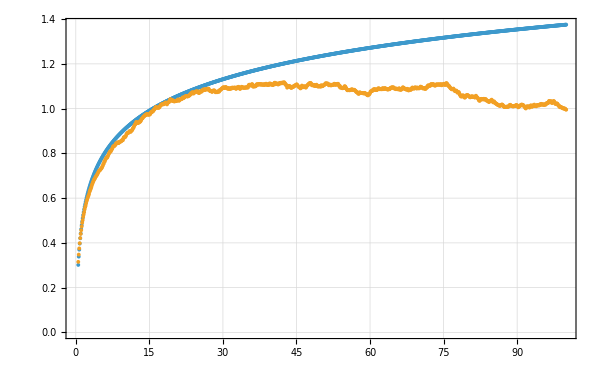

```mathematica
ListPlot[{theorySigma2,Transpose[{floquetSigma2Data[[1]],floquetSigma2Data[[2]]}]},PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

```mathematica
(*---3. COMPUTE SPECTRAL FORM FACTOR FROM PRECOMPUTED DATA---*)
tauLimit=2.0;
numPoints=500;
AbsoluteTiming[sffData=EnsembleSFFFromSpectra[ensembleSpectra,tauLimit,numPoints];]
```

{0.114664,Null}

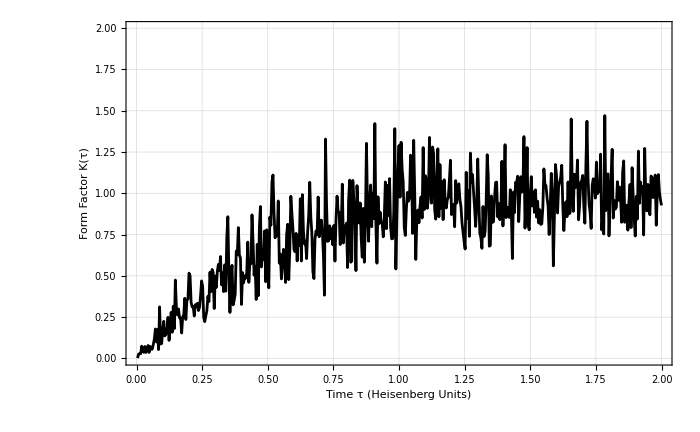

```mathematica
(*Plotting*)
Show[Plot[Kgoe[tau],{tau,0,tauLimit},PlotStyle->{Red,Thickness[0.007]}],ListPlot[Transpose[{sffData["TauDomain"],sffData["MeanSFF"]}],PlotStyle->{Black,PointSize[0.005]},Joined->True],Frame->True,FrameLabel->{"Time τ (Heisenberg Units)","Form Factor K(τ)"},GridLines->Automatic,PlotRange->{{0,tauLimit},{0,2}},ImageSize->700]
```

```mathematica
(*---3. COMPUTE SPECTRAL RIGIDITY (DELTA 3)---*)
AbsoluteTiming[floquetDelta3Data=EnsembleDelta3FromSpectra[ensembleSpectra,lTestDomain,mcSamples];]
```

{371.796,Null}

```mathematica
ClearAll[TheoryDelta3COE];
TheoryDelta3COE[L_]:=Piecewise[{(*Exact short-range Poisson/GOE limit*){L/15.0,0<=L<1.5},(*Dyson-Mehta exact asymptotic expansion for GOE/COE*){(1.0/Pi^2)*(Log[2.0*Pi*L]+EulerGamma-5.0/4.0-Pi^2/8.0),L>=1.5}}];
(*Map over your L domain*)
theoryDelta3={#,TheoryDelta3COE[#]}&/@lTestDomain;
```

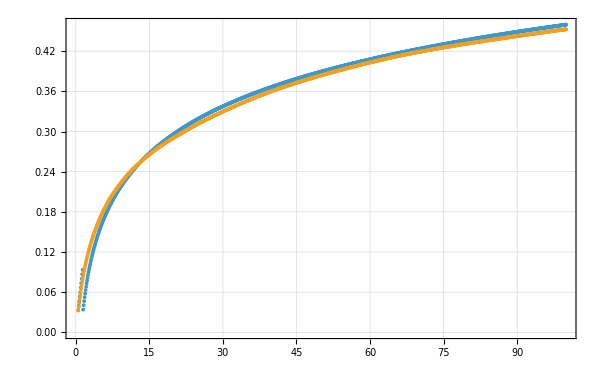

```mathematica
ListPlot[{theoryDelta3,Transpose[{floquetDelta3Data[[1]],floquetDelta3Data[[2]]}]},PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

## Test 2

```mathematica
(* ==============================================================*)(*STEP 1:EXTRACTION,UNFOLDING,VALIDATION*)(* ==============================================================*)
ClearAll[GetRawPhases,UnfoldLinear,ValidateUnfolding];

GetRawPhases[jParam_,alphaParam_,kParam_]:=Module[{mat,matM,eigs},mat=Floq[jParam,alphaParam,kParam];
matM=mat[[1;; ;;2,1;; ;;2]];
eigs=Eigenvalues[matM,Method->"Direct"];
Sort[Mod[Arg[eigs],2 Pi]]];

UnfoldLinear[phases_List]:=Module[{n=Length[phases]},<|"N"->n,"Phases"->phases,"Spectrum"->(n/(2 Pi))*phases|>];

ValidateUnfolding[specData_Association]:=Module[{phases,n,empiricalCDF,linearCDF,residuals,ks},phases=specData["Phases"];
n=specData["N"];
empiricalCDF=Range[n]/n;
linearCDF=phases/(2 Pi);
residuals=n (empiricalCDF-linearCDF);
ks=Max[Abs[residuals]]/Sqrt[n];
<|"Phases"->phases,"EmpiricalCDF"->empiricalCDF,"LinearCDF"->linearCDF,"Residuals"->residuals,"KS"->ks,"N"->n|>];
```

```mathematica
(*---Parameters and diagonalization---*)
J=1000;
alpha=0.84;
delta=0.01;
kCenter=20.;
SeedRandom[123];
kList=RandomReal[{kCenter-delta,kCenter+delta},100];
```

```mathematica
DistributeDefinitions[Floq];
```

```mathematica
Print["Diagonalizing..."];
AbsoluteTiming[rawPhases=ParallelTable[GetRawPhases[J,alpha,k],{k,kList},Method->"CoarsestGrained"];]
ensembleSpectra=Map[UnfoldLinear,rawPhases];
nDim=ensembleSpectra[[1]]["N"];
Print["N = ",nDim];
```

Diagonalizing...

{1994.68,Null}

N = 1001

```mathematica
(*---Staircase plot:3 sample realizations---*)
nReal=Length[ensembleSpectra];
sampleIdx=Round[Subdivide[1,nReal,2]];  (*{1,middle,last}*)
```

```mathematica
vd=Map[ValidateUnfolding,ensembleSpectra[[sampleIdx]]];
```

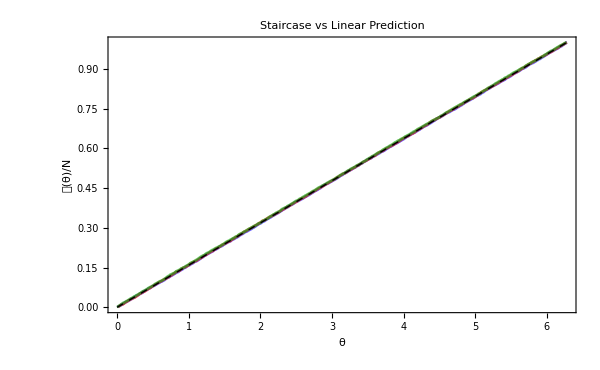

```mathematica
Show[Table[ListLinePlot[Transpose[{vd[[i]]["Phases"],vd[[i]]["EmpiricalCDF"]}],PlotStyle->{{Blue,Red,Darker[Green]}[[i]],Opacity[0.6]}],{i,3}],Plot[x/(2 Pi),{x,0,2 Pi},PlotStyle->{Black,Dashed,Thick}],Frame->True,FrameLabel->{"θ","𝒩(θ)/N"},PlotLabel->"Staircase vs Linear Prediction",ImageSize->600]
```

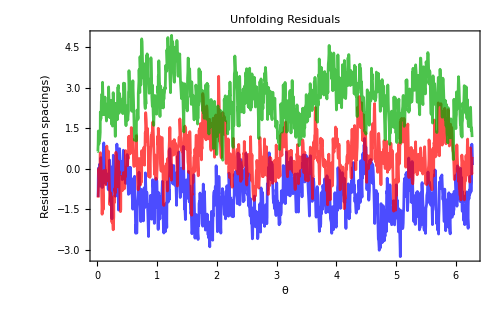

```mathematica
(*---Residuals in mean-spacing units---*)
Show[Table[ListLinePlot[Transpose[{vd[[i]]["Phases"],vd[[i]]["Residuals"]}],PlotStyle->{{Blue,Red,Darker[Green]}[[i]],Opacity[0.7]}],{i,3}],Frame->True,FrameLabel->{"θ","Residual (mean spacings)"},PlotLabel->"Unfolding Residuals",ImageSize->500,PlotRange->All]
```

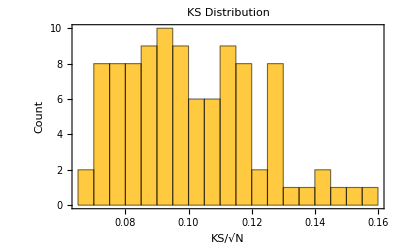

KS: mean = 0.1007, max = 0.1563

```mathematica
(*---KS across full ensemble---*)
allKS=Map[ValidateUnfolding[#]["KS"]&,ensembleSpectra];
Histogram[allKS,20,Frame->True,FrameLabel->{"KS/\!\(\*SqrtBox[\(N\)]\)","Count"},PlotLabel->"KS Distribution",ImageSize->400]
Print["KS: mean = ",NumberForm[Mean[allKS],4],", max = ",NumberForm[Max[allKS],4]];
```

```mathematica
(* ==============================================================*)(*STEP 2:NNSD—HISTOGRAM+CUMULATIVE (binning-independent)*)(* ==============================================================*)ClearAll[NNSpacings];
NNSpacings[specData_Association]:=Module[{s=specData["Spectrum"],n=specData["N"],diffs},diffs=Differences[s];
Append[diffs,n-Last[s]+First[s]]  (*wrap-around*)];
allSpacings=Sort[Flatten[Map[NNSpacings,ensembleSpectra]]];
```

```mathematica
(*---Analytical predictions:COE (beta=1)---*)
wignerCOE[s_]:=(Pi/2) s Exp[-Pi s^2/4];              (*linear repulsion*)
poissonP[s_]:=Exp[-s];

intWignerCOE[s_?NumericQ]:=NIntegrate[wignerCOE[t],{t,0,s}];
intPoisson[s_]:=1-Exp[-s];
```

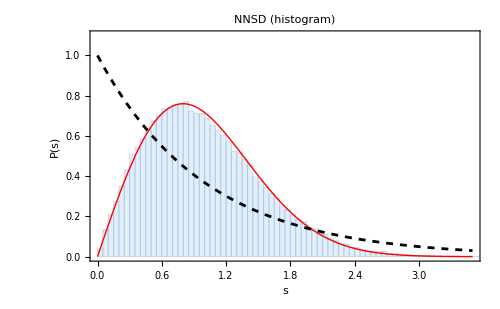

```mathematica
(*---2a.Histogram P(s)---*)
Show[Histogram[allSpacings,{0,4,0.05},"ProbabilityDensity",ChartStyle->Directive[LightBlue,EdgeForm[Gray]],PlotRange->{{0,3.5},{0,1.1}}],Plot[wignerCOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Plot[poissonP[s],{s,0,3.5},PlotStyle->{Black,Dashed}],Frame->True,FrameLabel->{"s","P(s)"},PlotLabel->"NNSD (histogram)",PlotLegends->Placed[{"COE surmise","Poisson"},{0.7,0.8}],ImageSize->500]
```

```mathematica
(*---2b.Cumulative I(s)---*)
nSpacings=Length[allSpacings];
empiricalCDF=Range[nSpacings]/nSpacings;
```

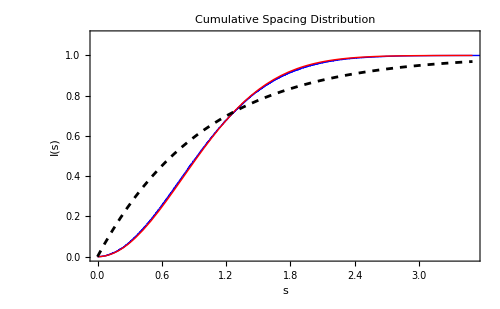

```mathematica
Show[ListLinePlot[Transpose[{allSpacings,empiricalCDF}],PlotStyle->{Blue,Thick},PlotRange->{{0,3.5},{0,1.1}}],Plot[intWignerCOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Plot[intPoisson[s],{s,0,3.5},PlotStyle->{Black,Dashed}],Frame->True,FrameLabel->{"s","I(s)"},PlotLabel->Style["Cumulative Spacing Distribution",20,Black],PlotLegends->Placed[{"Data","COE surmise","Poisson"},{0.75,0.4}],FrameStyle->Directive[Black,20],ImageSize->500]
```

```mathematica
(*---2c.Quantitative check---*)
Print["<s> = ",NumberForm[Mean[allSpacings],5],"  (expect 1.0)"];
Print["Var(s) = ",NumberForm[Variance[allSpacings],5],"  (COE surmise: ",NumberForm[N[4/Pi-1],4],")"];

cueCDFAtData=Map[intWignerCOE,allSpacings];
ksSpacings=Max[Abs[empiricalCDF-cueCDFAtData]];
Print["KS(data vs COE surmise) = ",NumberForm[ksSpacings,4]];
```

KS(data vs COE surmise) = 0.009204

```mathematica
(* ==============================================================*)(*STEP 3:NUMBER VARIANCE—SLIDING WINDOWS+DUAL ESTIMATOR*)(* ==============================================================*)ClearAll[CompileLevelCounter,ComputeSigma2Sliding,EvaluateSpectrumSigma2,EnsembleSigma2];

(*---Compiled binary search counter---*)
CompileLevelCounter[extendedSpectrum_List]:=Module[{packed,m},packed=Developer`ToPackedArray[N[extendedSpectrum]];
m=Length[packed];
Compile[{{z,_Real}},Module[{lo=1,hi=m,mid=0},While[lo<=hi,mid=Quotient[lo+hi,2];
If[packed[[mid]]<=z,lo=mid+1,hi=mid-1]];hi],CompilationTarget->"WVM",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->False]];

(*---Sigma2 via systematic sliding:one center per integer---*)
ComputeSigma2Sliding[counterFunc_,nLevels_Integer,lValues_List]:=Module[{validL,centers,nC},validL=Select[N[lValues],0<#<=(nLevels/2.0)&];
centers=N[Range[0,nLevels-1]];
nC=Length[centers];
Map[Function[{L},Module[{counts,s2theor,s2sample},counts=counterFunc[centers+L]-counterFunc[centers];
s2theor=Total[(counts-L)^2]/nC;
s2sample=Variance[counts];
{L,s2theor,s2sample}]],validL]];

(*---Per-spectrum evaluation---*)
EvaluateSpectrumSigma2[specData_Association,lValues_List]:=Module[{ext,counter},ext=Join[specData["Spectrum"]-specData["N"],specData["Spectrum"],specData["Spectrum"]+specData["N"]];
counter=CompileLevelCounter[ext];
ComputeSigma2Sliding[counter,specData["N"],lValues]];

(*---Ensemble average with dual estimator---*)
EnsembleSigma2[spectraList_List,lValues_List]:=Module[{nMat,allResults,effectiveL,theorVals,sampleVals,meanTheor,seTheor,meanSample,seSample},nMat=Length[spectraList];
DistributeDefinitions[CompileLevelCounter,ComputeSigma2Sliding,EvaluateSpectrumSigma2];
allResults=ParallelTable[EvaluateSpectrumSigma2[spectraList[[i]],lValues],{i,nMat},Method->"CoarsestGrained"];
effectiveL=allResults[[1,All,1]];
theorVals=Map[#[[All,2]]&,allResults];
sampleVals=Map[#[[All,3]]&,allResults];
meanTheor=Mean[theorVals];
seTheor=StandardDeviation[theorVals]/Sqrt[nMat*1.0];
meanSample=Mean[sampleVals];
seSample=StandardDeviation[sampleVals]/Sqrt[nMat*1.0];
<|"LValues"->effectiveL,"Sigma2TheorMean"->meanTheor,"SETheorMean"->seTheor,"Sigma2SampleMean"->meanSample,"SESampleMean"->seSample|>];
```

```mathematica
(*---Compute---*)
lDomain=Range[0.5,200.0,0.5];

Print["Computing number variance..."];
AbsoluteTiming[sigma2Result=EnsembleSigma2[ensembleSpectra,lDomain];]
```

Computing number variance...

{219.674,Null}

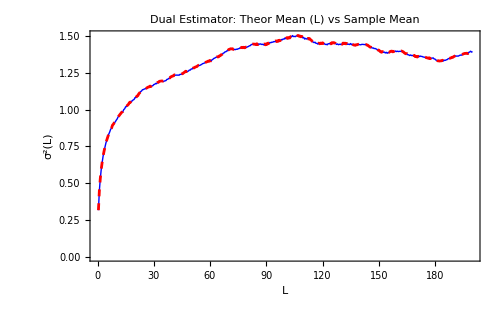

```mathematica
(*---3a.Dual estimator comparison---*)
Show[ListLinePlot[{Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2TheorMean"]}],Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2SampleMean"]}]},PlotStyle->{{Blue,Thick},{Red,Dashed}},PlotRange->All],Frame->True,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Dual Estimator: Theor Mean (L) vs Sample Mean",PlotLegends->Placed[{"Theor mean","Sample mean"},{0.3,0.8}],ImageSize->500]
```

```mathematica
(*---3a.Dual estimator comparison---*)
Show[ListLinePlot[{Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2TheorMean"]}],Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2SampleMean"]}]},PlotStyle->{{Blue,Thick},{Red,Dashed}},PlotRange->All],Frame->True,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},PlotLabel->"Dual Estimator: Theor Mean (L) vs Sample Mean",PlotLegends->Placed[{"Theor mean","Sample mean"},{0.3,0.8}],ImageSize->500]
```

-Graphics-

```mathematica
(*---COE asymptotic prediction (valid for 1 <<L <<N)---*)
gamma=EulerGamma;
sigma2COEAsymptotic[L_]:=(2/Pi^2) (Log[2 Pi L]+1+gamma-Pi^2/8);
```

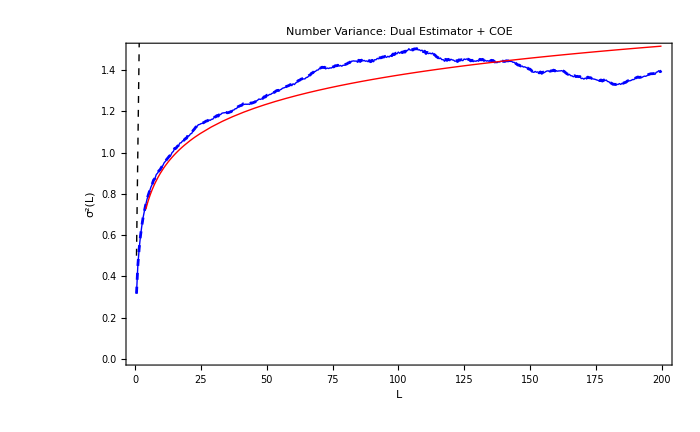

```mathematica
(*---3a.Dual estimator+COE+Poisson---*)
Show[ListLinePlot[{Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2TheorMean"]}],Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2SampleMean"]}]},PlotStyle->{{Blue,Thick},{Blue,Dashed}},PlotRange->All],Plot[sigma2COEAsymptotic[L],{L,0.5,Max[sigma2Result["LValues"]]},PlotStyle->{Red,Thick}],Plot[L,{L,0.5,Max[sigma2Result["LValues"]]},PlotStyle->{Black,Dashed,Thin}],Frame->True,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},FrameStyle->Directive[Black,20],PlotLabel->Style["Number Variance: Dual Estimator + COE",18,Black],PlotLegends->Placed[{"Theor mean","Sample mean","COE (asymptotic)","Poisson"},{0.3,0.75}],PlotRange->{All,{0,1.5}},ImageSize->700]
```

## COE

```mathematica
(* ==============================================================*)(*STEP 4:COE REFERENCE BY DIRECT SIMULATION*)(* ==============================================================*)ClearAll[RandomCOEUnfolded];

RandomCOEUnfolded[n_Integer]:=Module[{z,q,r,diag,cue,sym,eigs,phases},(*Haar CUE via QR of complex Ginibre*)
z=RandomVariate[NormalDistribution[],{n,n}]+I*RandomVariate[NormalDistribution[],{n,n}];
{q,r}=QRDecomposition[z];
diag=DiagonalMatrix[Sign[Diagonal[r]]];
cue=diag.q;(*proper Haar CUE*)(*COE=U.U^T*)sym=cue.Transpose[cue];
eigs=Eigenvalues[sym];
phases=Sort[Mod[Arg[eigs],2 Pi]];
<|"N"->n,"Phases"->phases,"Spectrum"->(n/(2 Pi))*phases|>];
```

```mathematica
(*Quick sanity:check one realization*)
testCOE=RandomCOEUnfolded[nDim];
Print["COE test: N = ",testCOE["N"],", phase range = [",Min[testCOE["Phases"]],", ",Max[testCOE["Phases"]],"]"];
```

COE test: N = 501, phase range = [0.00593164, 6.27601]

```mathematica
(*Generate COE ensemble*)
nCOE=100;  (*more realizations since they're cheap*)
Print["Generating ",nCOE," COE matrices of dimension ",nDim,"..."];
AbsoluteTiming[coeSpectra=Table[RandomCOEUnfolded[nDim],{nCOE}];]
```

Generating 100 COE matrices of dimension 501...

{51.5128,Null}

```mathematica
(*Compute Sigma2 for COE ensemble using identical pipeline*)
Print["Computing COE number variance..."];
AbsoluteTiming[sigma2COE=EnsembleSigma2[coeSpectra,lDomain];]
```

Computing COE number variance...

{40.012,Null}

```mathematica
gamma=EulerGamma;
sigma2COEAsymptotic[L_]:=(2/Pi^2) (Log[2 Pi L]+1+gamma-Pi^2/8);
```

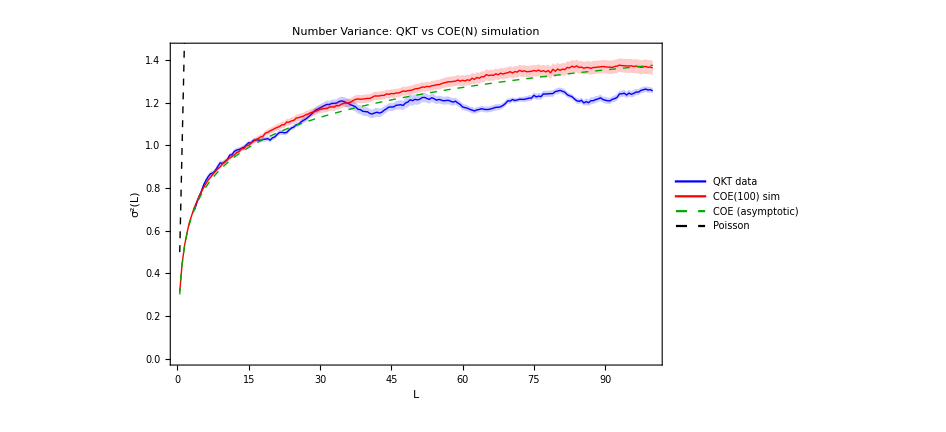

```mathematica
Show[ListLinePlot[{Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2TheorMean"]+sigma2Result["SETheorMean"]}],Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2TheorMean"]-sigma2Result["SETheorMean"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],Blue]],(*Data*)ListLinePlot[Transpose[{sigma2Result["LValues"],sigma2Result["Sigma2TheorMean"]}],PlotStyle->{Blue,Thick}],(*Error band for COE sim*)ListLinePlot[{Transpose[{sigma2COE["LValues"],sigma2COE["Sigma2TheorMean"]+sigma2COE["SETheorMean"]}],Transpose[{sigma2COE["LValues"],sigma2COE["Sigma2TheorMean"]-sigma2COE["SETheorMean"]}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],Red]],(*COE simulation*)ListLinePlot[Transpose[{sigma2COE["LValues"],sigma2COE["Sigma2TheorMean"]}],PlotStyle->{Red,Thick}],(*COE asymptotic*)Plot[sigma2COEAsymptotic[L],{L,0.5,Max[lDomain]},PlotStyle->{Darker[Green],Thick,Dashed}],(*Poisson*)Plot[L,{L,0.5,Max[lDomain]},PlotStyle->{Black,Dashed,Thin}],Frame->True,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(L)"},FrameStyle->Directive[Black,20],PlotLabel->"Number Variance: QKT vs COE(N) simulation",LabelStyle->Directive[Black,20],PlotRange->{All,{0,1.45}},ImageSize->700,Epilog->Inset[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick],Directive[Darker[Green],Thick,Dashed],Directive[Black,Dashed,Thin]},{"QKT data","COE("<>ToString[nCOE]<>") sim","COE (asymptotic)","Poisson"},LegendMarkerSize->20,LabelStyle->Directive[Black,14]],Scaled[{0.85,0.3}]]]
```

```mathematica
(*---4b.Residual:data minus COE---*)
residual=sigma2Result["Sigma2TheorMean"]-sigma2COE["Sigma2TheorMean"];
seTotal=Sqrt[sigma2Result["SETheorMean"]^2+sigma2COE["SETheorMean"]^2];
```

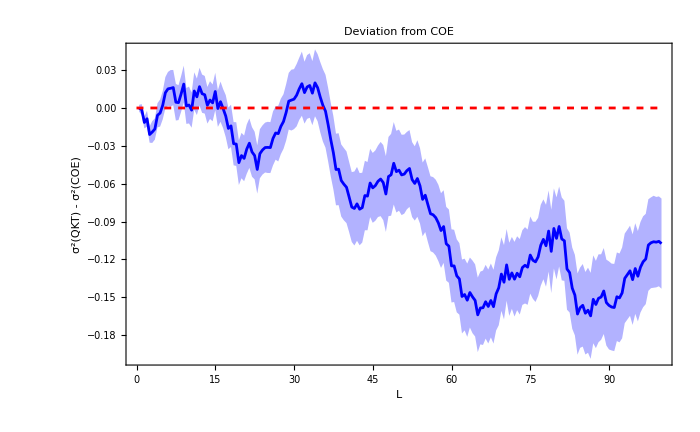

```mathematica
Show[ListLinePlot[{Transpose[{sigma2Result["LValues"],residual+seTotal}],Transpose[{sigma2Result["LValues"],residual-seTotal}]},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],Blue]],ListLinePlot[Transpose[{sigma2Result["LValues"],residual}],PlotStyle->{Blue}],Plot[0,{x,0,Max[lDomain]},PlotStyle->{Red,Dashed}],Frame->True,FrameLabel->{"L","\!\(\*SuperscriptBox[\(σ\), \(2\)]\)(QKT) - \!\(\*SuperscriptBox[\(σ\), \(2\)]\)(COE)"},PlotLabel->"Deviation from COE",LabelStyle->Directive[Black, 20],ImageSize->700]
```

# No separation

```mathematica
pdf[r_,β_]:=((r+r^2)^β)/((1+r+r^2)^(1+3β/2));
```

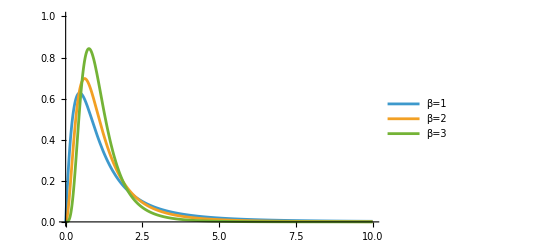

```mathematica
plotpdf=Plot[{(27/8)pdf[x,1],(81/4)(Sqrt[3]/Pi)pdf[x,2],(729/4)(Sqrt[3]/Pi)pdf[x,4]},{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->{"β=1","β=2","β=3"}]
```

```mathematica
Clear[J];
J=500;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Clear[Floqa];
Floqa[a_,b_,c_]:=N[MatrixExp[(-I*c/(2J))(ops[[4]])].MatrixExp[(-I*a)(ops[[3]])]];
Clear[Floqb];
Floqb[a_,b_,c_]:=N[MatrixExp[(-I*c/(2J))(ops[[4]])].MatrixExp[-I*a*ops[[3]]-I*b*ops[[2]]]];
```

```mathematica
blist={0.001,0.1,0.5,1.0};
```

```mathematica
a=Pi/2.;
c=20.0;
b=0.;
```

```mathematica
mat=Floqa[a,b,c];
{eigenval,eigenvec}=Eigensystem[mat];
```

```mathematica
Clear[rk];
rk[list_,k_]:=Table[(list[[i+2k]]-list[[i+k]])/(list[[i+k]]-list[[i]]),{i,1,Length[list]-2k}];
```

```mathematica
quasi=Sort[Arg[eigenval]]+Pi;
```

```mathematica
gaps1=rk[quasi,1];
gaps2=rk[quasi,2];
gaps4=rk[quasi,4];
```

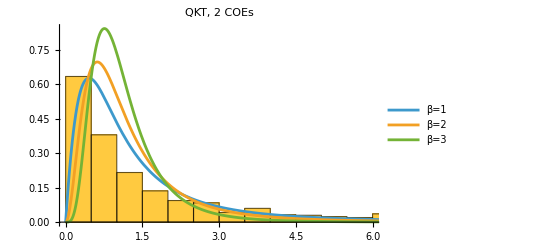

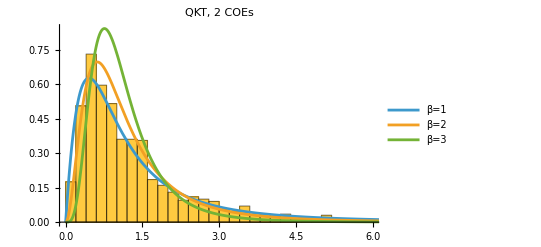

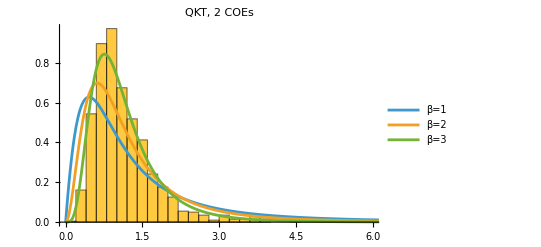

```mathematica
Show[{Histogram[gaps1,Automatic,"PDF",PlotRange->{{0,6},Automatic},PlotLabel->Style["QKT, 2 COEs",20,Black]],plotpdf}]
Show[{Histogram[gaps2,Automatic,"PDF",PlotRange->{{0,6},Automatic},PlotLabel->Style["QKT, 2 COEs",20,Black]],plotpdf}]
Show[{Histogram[gaps4,Automatic,"PDF",PlotRange->{{0,6},Automatic},PlotLabel->Style["QKT, 2 COEs",20,Black]],plotpdf}]
```

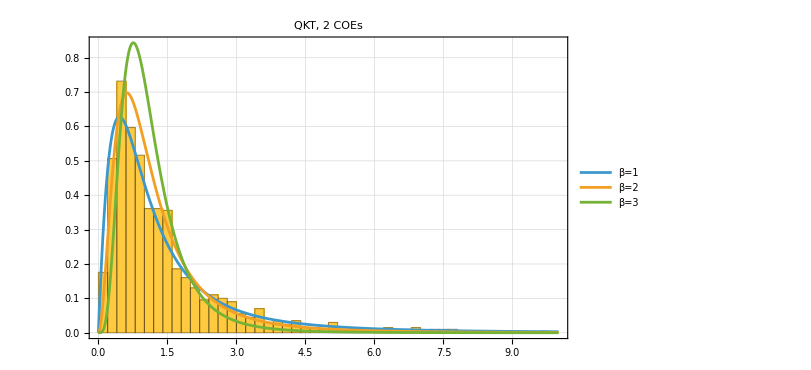

```mathematica
plot=Show[{Histogram[gaps2,Automatic,"PDF",PlotRange->{{0,10},Automatic},PlotLabel->Style["QKT, 2 COEs",20,Black],PlotTheme->"Detailed",ImageSize->600,FrameStyle->Directive[Black,18]],plotpdf}]
```